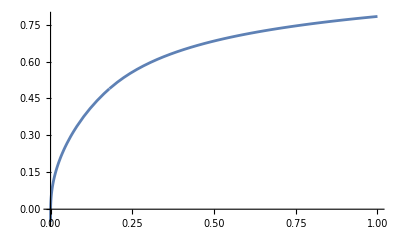

(3/5)^(5/6)/2^(5/12)+(12 5^(1/3) Log[(50 x)/9])/((10+normLog2Max) Log[2] (25+(24 √15 (Log[(50 x)/9]/((10+normLog2Max) If[(10+normLog2Max) Log[(50 x)/9]<0,-equationScale[1.-xPivot,1.-yPivot,kPower,kSlope],equationScale[xPivot,yPivot,kPower,kSlope]]))^(3/2))/Log[2]^(3/2))^(2/3))

(3/5)^(5/6)/2^(5/12)+(12 5^(1/3) Log[(50 x)/9])/((10+normLog2Max) Log[2] (25+(24 √15 (Log[(50 x)/9]/((10+normLog2Max) If[(10+normLog2Max) Log[(50 x)/9]<0,-equationScale[1.-xPivot,1.-yPivot,kPower,kSlope],equationScale[xPivot,yPivot,kPower,kSlope]]))^(3/2))/Log[2]^(3/2))^(2/3))

0.4894370895738783411+(29.60368581971857529 Log[5.5555555555555555556 x])/((10.+normLog2Max) (25.+161.0714913007129981 (Log[5.5555555555555555556 x]/((10.+normLog2Max) If[(10.+normLog2Max) Log[5.5555555555555555556 x]<0,-1. equationScale[1.-1. xPivot,1.-1. yPivot,kPower,kSlope],equationScale[xPivot,yPivot,kPower,kSlope]]))^(3/2))^(2/3))

0.4894370895738783411+(29.60368581971857529 Log[5.5555555555555555556 x])/((10.+normLog2Max) (25.+161.0714913007129981 (Log[5.5555555555555555556 x]/((10.+normLog2Max) If[(10.+normLog2Max) Log[5.5555555555555555556 x]<0,-1. equationScale[1.-1. xPivot,1.-1. yPivot,kPower,kSlope],equationScale[xPivot,yPivot,kPower,kSlope]]))^(3/2))^(2/3))

```mathematica
(*Agx Config*)
kNormLog2Min=Rationalize[-10.0];
kMidGray=Rationalize[0.18];
kPower=Rationalize[1.5];
kSlope=Rationalize[2.4];

(*AgX*)
equationScale[transitionX_,transitionY_, power_, slope_]:=Module[
{termA, termB},
termA = (slope*(Rationalize[1.0-transitionX]))^(Rationalize[-1.0*power]);
termB =  SetPrecision[((slope*(Rationalize[1.0-transitionX]))/(Rationalize[1.0 - transitionY]))^(power) - 1.0, 20];
 (termA * termB)^(Rationalize[-1.0 / power])
];

exponentialCurve[x_,scaleInput_, xPivot_, yPivot_, power_, slope_]:=(scaleInput * exponential[(slope*(x-xPivot))/scaleInput, power])+yPivot

exponential[x_, power_]:=x / ((1+(x^power))^(1/power))

logEncodingLog2[lin_, normLog2Max_]:=Module[{lg2},
lg2=Log2[lin/kMidGray];
(lg2-kNormLog2Min)/(normLog2Max-kNormLog2Min)];

calculateSigmoid[x_, normLog2Max_]:= Module[{scaleValue,logEncodedX},
logEncodedX=logEncodingLog2[x,normLog2Max];

xPivot=Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min);
yPivot=kMidGray^(Rationalize[1.0/2.4]);

scaleValue = If[logEncodedX<xPivot,-1*equationScale[1.0-xPivot,1.0-yPivot,kPower, kSlope],equationScale[xPivot,yPivot,kPower, kSlope]];exponentialCurve[logEncodedX,scaleValue, xPivot,yPivot, kPower, kSlope]
];

(*Calculate OpenColorIO allocation for log2 from open domain \\ tristimulus value*)
calculateOCIOLog2[inEV_,odMiddleGrey_]:=Log2[2^inEV*odMiddleGrey];

(*Debug*)
Plot[calculateSigmoid[x, 6.5],{x,0,1}]

Assuming[x>=0&&logEncodedX>=(Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min)) ,Simplify[calculateSigmoid[x,normLog2Max]]]
Assuming[x>=0&&logEncodedX<Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min),Simplify[calculateSigmoid[x, normLog2Max]]]
Assuming[x>=0&&logEncodedX>=Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min),N[Simplify[calculateSigmoid[x, normLog2Max]],20]]
Assuming[x>=0&&logEncodedX<Abs[kNormLog2Min]/(normLog2Max-kNormLog2Min),N[Simplify[calculateSigmoid[x, normLog2Max]],20]]
(*N[calculateOCIOLog2[kNormLog2Min,Rationalize[kMidGray]],20]
N[calculateOCIOLog2[kMaxEV,Rationalize[kMidGray]],20]*)
```